### Variance

```mathematica
Integrate[k^(d-1)/((k^2+1/L^2)^(H+d/2)),{k,0,∞},Assumptions->{L>0,0<H<1,d>0}]
```

(L^(2 H) Gamma[d/2] Gamma[H])/(2 Gamma[d/2+H])

```mathematica
Integrate[k^(-2H-1),{k,1,∞}]
```

ConditionalExpression[1/(2 H), Re[H]>0]

### Velocity Gradient Variance

1d

```mathematica
Integrate[k^2/((k^2+1/L^2)^(H+1/2)),{k,-∞,∞},Assumptions->{L>0}]
```

ConditionalExpression[(L^(-2+2 H) √π Gamma[-1+H])/(2 Gamma[1/2+H]), Re[H]>1]

```mathematica
Integrate[k^(d+1)/((k^2+1/L^2)^(H+d/2)),{k,0,∞},Assumptions->{L>0,d>0}]
```

ConditionalExpression[(L^(-2+2 H) Gamma[1+d/2] Gamma[-1+H])/(2 Gamma[d/2+H]), Re[H]>1]

### Velocity Gradient Variance, Regularized FGF

1d

```mathematica
Clear[n]
```

```mathematica
With[{n=2},Integrate[k^2/((k^2+1/L^2)^(H+1/2))Exp[-(2ν(2π √(k^2))^n)/n],{k,-∞,∞},Assumptions->{L>0,n>1,ν>0}]]
```

(L^(-2+2 H) √π Gamma[-1+H] Hypergeometric1F1[3/2,2-H,(4 π^2 ν)/L^2])/(2 Gamma[1/2+H])+(2 π)^(2 (-1+H)) ν^(-1+H) Gamma[1-H] Hypergeometric1F1[1/2+H,H,(4 π^2 ν)/L^2]

```mathematica
With[{n=3},Integrate[k^2/((k^2+1/L^2)^(H+1/2))Exp[-(2ν(2π √(k^2))^n)/n],{k,-∞,∞},Assumptions->{L>0,n>1,ν>0}]]
```

(3^(1/3 (-14+H)) (2^(2/3) 3^(19/6+(2 H)/3) L^(3+2 H) π^(5/2) ν^(2/3) Gamma[-5/2+H] Gamma[1/3 (-1+H)] Gamma[H/3] Gamma[(1+H)/3] HypergeometricPFQ[{5/6,7/6},{2/3-H/3,1-H/3,4/3-H/3},-(64 π^6 ν^2)/(9 L^6)]+81 2^(8 H/3) 3^(1/3) L^5 π^(2 H) ν^(2 H/3) Gamma[1/6+H/3] Gamma[1/2+H/3] Gamma[5/6+H/3] Gamma[-5/2+H] Gamma[-2/3 (-1+H)] HypergeometricPFQ[{1/2+H/3,5/6+H/3},{1/3,2/3,2/3+H/3},-(64 π^6 ν^2)/(9 L^6)]+2 2^(1/3) π^2 Gamma[-5/6+H/3] Gamma[-1/2+H/3] Gamma[-1/6+H/3] (-2^(1/3+(8 H)/3) 3^(2/3) (1+2 H) L^3 π^(2 H) ν^((2 (1+H))/3) Gamma[-(2 H)/3] Gamma[1/2+H] HypergeometricPFQ[{5/6+H/3,7/6+H/3},{2/3,4/3,1+H/3},-(64 π^6 ν^2)/(9 L^6)]+2^(1+(8 H)/3) (3+8 H+4 H^2) L π^(2+2 H) ν^((2 (2+H))/3) Gamma[1/2+H] Gamma[-2/3 (1+H)] HypergeometricPFQ[{7/6+H/3,3/2+H/3},{4/3,5/3,4/3+H/3},-(64 π^6 ν^2)/(9 L^6)]-32 2^(1/3) 3^((2 (1+H))/3) L^(2 H) π^3 ν^(5/3) Gamma[-5/2+H] HypergeometricPFQ[{1,4/3,5/3},{3/2,7/6-H/3,3/2-H/3,11/6-H/3},-(64 π^6 ν^2)/(9 L^6)])))/(4 2^(2/3) L^5 π^3 ν^(2/3) Gamma[-5/2+H] Gamma[1/2+H])

```mathematica
Integrate[k^(d+1)/((k^2+1/L^2)^(H+d/2)),{k,0,∞},Assumptions->{L>0,d>0}]
```

ConditionalExpression[(L^(-2+2 H) Gamma[1+d/2] Gamma[-1+H])/(2 Gamma[d/2+H]), Re[H]>1]

### Second Order Structure Function

```mathematica
Integrate[k^(-2H-1)(1-Cos[2π k]),{k,0,1}]
```

ConditionalExpression[(2 π^2 HypergeometricPFQ[{1-H},{3/2,2-H},-π^2])/(2 H-2 H^2), Re[H]<1]

```mathematica
Integrate[k^(-2H-1)(1-Cos[k x]),{k,0,1},Assumptions->x∈Reals]
```

ConditionalExpression[(-1+HypergeometricPFQ[{-H},{1/2,1-H},-x^2/4])/(2 H), Re[H]<1]

```mathematica
Integrate[k^(-2H+1),{k,0,1}]
```

ConditionalExpression[1/(2-2 H), Re[H]<1]

We want to solve the integral
2(1-Cos(2 pi y_1))/|y|^{2H+d} over all of R^d
which can be done in spherical coordinates

```mathematica
(* 1 d *)
```

```mathematica
2Integrate[(1-Cos[2π k])/((k^2)^(H+1/2)),{k,-∞,∞},Assumptions->0<H<1]
```

-2^(2+2 H) π^(2 H) Cos[H π] Gamma[-2 H]

```mathematica
FullSimplify[Cos[π H]/Sin[2π H]]
```

1/2 Csc[H π]

```mathematica
(* 2d *)
```

```mathematica
Integrate[(1-Cos[2π r Cos[θ]]),{θ,0,2π},Assumptions->r>0]
```

2 (π-π BesselJ[0,2 π r])

```mathematica
2 Integrate[2 (π-π BesselJ[0,2 π r])r/r^(2H+2),{r,0,∞}]
```

ConditionalExpression[-(2 π^(1+2 H) Gamma[-H])/Gamma[1+H], 0<Re[H]<1]

```mathematica
-(2 π^(1+2 H) Gamma[-H])/Gamma[1+H]//TeXForm
```

-\frac{2 \pi ^{2 H+1} \Gamma (-H)}{\Gamma
   (H+1)}

```mathematica
FullSimplify[Gamma[-H]/Gamma[1+H]]
```

Gamma[-H]/Gamma[1+H]

```mathematica
(* 3 d *)
```

```mathematica
Integrate[Sin[ϕ1](1-Cos[2π r Cos[ϕ1]]),{ϕ1,0,π},Assumptions->{r>0}]
```

2-Sin[2 π r]/(π r)

```mathematica
2 Integrate[(2-Sin[2 π r]/(π r))r^2/r^(2H+3),{r,0,∞},Assumptions->0<H<1]
```

2^(2+2 H) π^(2 H) Cos[H π] Gamma[-1-2 H]

```mathematica
FullSimplify[Cos[π H]/Sin[π+π 2 H]]
```

-1/2 Csc[H π]

```mathematica
(* n-d *)
```

```mathematica
Integrate[Sin[ϕ1]^(d-2)(1-Cos[2π r Cos[ϕ1]]),{ϕ1,0,π},Assumptions->{r>0,d>2}]
```

-(√π Gamma[1/2 (-1+d)] (-1+Hypergeometric0F1[d/2,-π^2 r^2]))/Gamma[d/2]

```mathematica
2Integrate[(-1/Gamma[d/2] √π Gamma[1/2 (-1+d)] (-1+Hypergeometric0F1[d/2,-π^2 r^2]))r^(-1-2H),{r,0,∞},Assumptions->{d>2,H<1}]
```

ConditionalExpression[-(π^(1/2+2 H) Gamma[1/2 (-1+d)] Gamma[-H])/Gamma[d/2+H], H>0]

```mathematica
Integrate[Sin[ϕ]^(d-n-1),{ϕ,0,π},Assumptions->{d>n}]
```

(√π Gamma[(d-n)/2])/Gamma[1/2 (1+d-n)]

```mathematica
%//TraditionalForm
```

(√π (d-n)/2)/(1/2 (d-n+1))

```mathematica
(* 3d from high dim integrals *)
fh[H_]=-2π(π^(1/2+2 H) Gamma[1/2 (-1+d)] Gamma[-H])/Gamma[d/2+H]/.d->3
```

-(2 π^(3/2+2 H) Gamma[-H])/Gamma[3/2+H]

```mathematica
2π(-(2 π^(3/2+2 H) Gamma[-H])/Gamma[3/2+H])
```

```mathematica
(* 3d from spherical coordinates *)
```

```mathematica
fs[H_]:=2π 2^(2+2 H) π^(2 H) Cos[H π] Gamma[-1-2 H]
```

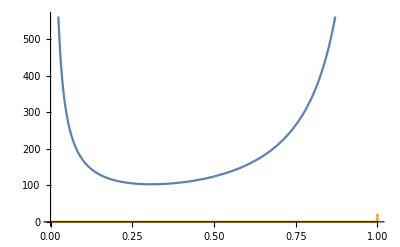

```mathematica
Plot[{fs[H],fs[H]-fh[H]},{H,0,1}]
```

```mathematica
a=.5*Sqrt[12]
```

1.73205

```mathematica
(* nd *)
```

```mathematica
(* variance, 1d *)
```

```mathematica
Integrate[(k^2+ε^2)^(-H-1/2),{k,-∞,∞},Assumptions->{ε>0,0<H<1}]
```

(√π ε^(-2 H) Gamma[H])/Gamma[1/2+H]

```mathematica
(* variance, 2d *)
```

```mathematica
Integrate[k(k^2+ε^2)^(-H-2/2),{k,0,∞},Assumptions->{ε>0,0<H<1}]
```

ε^(-2 H)/(2 H)

```mathematica
(* times 2π *)
```

```mathematica
(* variance, general d *)
```

```mathematica
Integrate[k^(d-1)(k^2+ε^2)^(-H-d/2),{k,0,∞},Assumptions->{ε>0,0<H<1,d>2}]
```

(ε^(-2 H) Gamma[d/2] Gamma[H])/(2 Gamma[d/2+H])

```mathematica
(* times the n-surface S_{n-1} *)
```

```mathematica
(2 π^(d/2))/Gamma[d/2](ε^(-2 H) Gamma[d/2] Gamma[H])/(2 Gamma[d/2+H])
```

(π^(d/2) ε^(-2 H) Gamma[H])/Gamma[d/2+H]